```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

# Ternary Diagrams

Testing different methods to make ternary diagrams from https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots

## The Challenge

Plot this function as a ternary plot:

```mathematica
f=#3 Sin[10 #1]^2+(1-#3) #3 Cos[20 #2]^2&;
```

## Approach 1: Starting with a 3D plot

https://mathematica.stackexchange.com/a/46652/60546

```mathematica
frange=Through@{NMinValue,NMaxValue}[{f[x,y,z],0≤x≤1&&0≤y≤1&&0≤z≤1},{x,y,z}];
```

```mathematica
AbsoluteTiming[trigplot3d=ContourPlot3D[x+y+z==1,{x,0,1},{y,0,1},{z,0,1},PlotRange->All,PlotPoints->50,(*you can add any kind of mesh:*)MeshFunctions->Function[{x,y,z,w},f[x,y,z]],Mesh->10,(*ColorFunction is essential:*)ColorFunctionScaling->False,ColorFunction->Function[{x,y,z,w},ColorData["Rainbow"][Rescale[f[x,y,z],frange]]]]]
```

{0.49057,-Graphics3D-}

```mathematica
pt3d={VertexNormals,BoxRatios,Lighting,RotationAction,SphericalRegion};
optboth={PlotRange,PlotRangePadding};
```

```mathematica
trigplot2d=trigplot3d/.GraphicsComplex[pts_,others__]:>GraphicsComplex[#+{1/2,1/(2 Sqrt[3])}&/@(((pts/Sqrt[2]).RotationMatrix[{{1,1,1},{0,0,1}}]ᵀ)[[All,1;;2]].RotationMatrix[-((3 π)/4)]ᵀ),others]/.Rule[opt_,_]/;MemberQ[opt3d,opt]:>Sequence[]/.Rule[opt_,v_]/;MemberQ[optboth,opt]:>Rule[opt,v[[1;;2]]]/.Graphics3D->Graphics;
```

The tick function:

```mathematica
ClearAll[tickGraphics,triangleTicks];Module[{ticklen=0.025,(*length of ticks (const parameter)*)textoffset=0.04},tickGraphics[tickrange:{0.,total_},angle_]:=With[{rotSideXF=RotationTransform[angle,total {1.,Tan[Pi/6]}/2.]},{Line[rotSideXF/@Thread[{tickrange,0}]],With[{rotTickXF=Composition[RotationTransform[π/3.,rotSideXF@{#,0.}],rotSideXF]},{Text[NumberForm[N@#,{3,2}],rotTickXF[total {-ticklen-textoffset,0}+{#,0.}],{0,0.}],{Line[rotTickXF/@{total {-ticklen,0}+{#,0.},{#,0.}}]}}]&/@Select[N@FindDivisions[tickrange,4],0.≤#≤total&]}];
triangleTicks[g_Graphics,total_: 1]:=Show[Graphics[First@g],Graphics[{AbsoluteThickness[0.5],Table[tickGraphics[{0.,total},N@angle],{angle,0,4 Pi/3,2 Pi/3}]}],Axes->False,Frame->None,PlotRange->total {{0,1+ticklen},{0,Sqrt[3]/2+ticklen/2}},PlotRangePadding->0.07 total,PlotRangeClipping->False,ImagePadding->{{20,5},{20,5}}]]
```

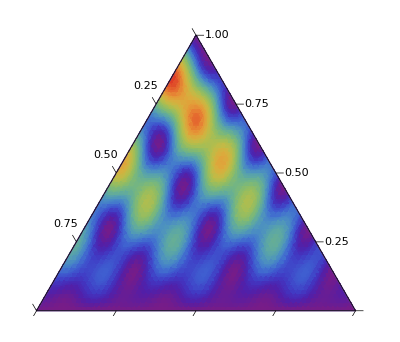

```mathematica
triangleTicks[trigplot2d]
```

## Approach 2: Starting with a 2D plot

https://mathematica.stackexchange.com/a/39751/60546

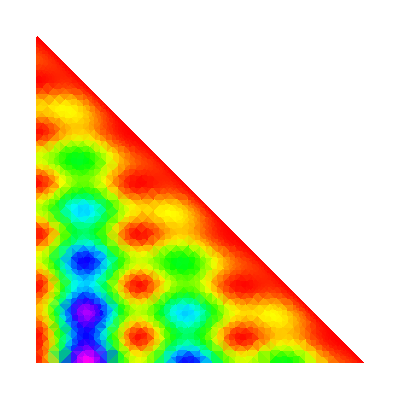

```mathematica
dp=DensityPlot[f[x,y,1-x-y],{x,0,1},{y,0,1},RegionFunction->(#1≤1-#2&),ColorFunction->(Hue[0.85 #]&),Frame->None,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
{error,xf}=FindGeometricTransform[{{0,0},{1,0},{1,Tan[Pi/3]}/2},{{0,0},{1,0},{0,1}}];
```

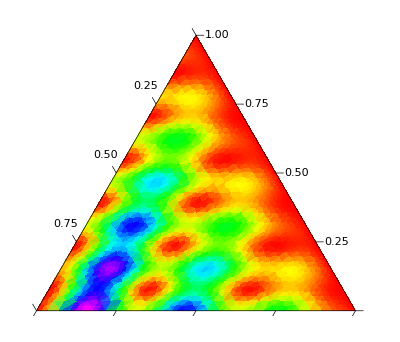

```mathematica
triangleTicks[Graphics[GeometricTransformation[First@dp,xf]]]
```

## Approach 3: Texture rendering

https://mathematica.stackexchange.com/a/39738/60546

```mathematica
texturize[f_,n_,colf_]:=#/.Polygon[{v1_,v2_,v3_}]:>{EdgeForm[],Texture@ImageData@Colorize[Image@f[#1,#2,1-#1-#2]&[#,Transpose[#]]&@ConstantArray[Range[-1./n,1+1/n,1./n],n+3],ColorFunction->colf,ColorFunctionScaling->False],Polygon[{v1,v2,v3},VertexTextureCoordinates->{{1-1.5/(n+3),1-1.5/(n+3)},{1.5/(n+3),1.5/(n+3)},{1.5/(n+3),1-1.5/(n+3)}}]}&;
```

```mathematica
f=#3 Sin[10 #1]^2+(1-#3) #3 Cos[20 #2]^2&;
```

```mathematica
triangleTicks@Graphics@N@Polygon[{{0,0},{1,0},{1/2,Sqrt[3]/2}}] //texturize[f,300,Hue]
```

-Graphics-

## Approach 4: Update of approach 2

https://mathematica.stackexchange.com/a/39751/60546

```mathematica
cartestianToBarycentric2=Compile[{{x,_Real},{y,_Real}},(x-y) {1,0}+y {1,Sqrt[3]}/2,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
base=DensityPlot[f[x-y,y,1-x],{x,0,1},{y,0,1},Mesh->All,MaxRecursion->0,RegionFunction->(#1≥#2&),ColorFunction->(Hue[0.85 #]&),Frame->None,PlotRange->All,AspectRatio->Automatic];
```

```mathematica
transformed=MapAt[cartestianToBarycentric2@@Transpose[#]&,base,{1,1}];
```

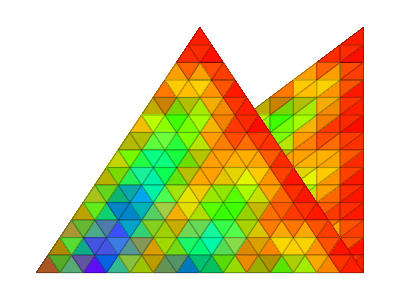

```mathematica
Graphics[{Inset[Show[base,AlignmentPoint->{1.2,0}],{0,0},Automatic,1],Thick,Arrow[{{-0.1,0.4},{0.1,0.4}}],Inset[Show[transformed,AlignmentPoint->{-0.1,0}],{0,0},Automatic,1]},PlotRange->{{-1.2,1.15},{-0.05,1.0}}]
```

```mathematica
dp=DensityPlot[f[x-y,y,1-x],{x,0,1},{y,0,1},MeshFunctions->{#1-#2&,#2&,1-#1&},Mesh->19,RegionFunction->(#1≥#2&),ColorFunction->(Hue[0.85 #]&),Frame->None,PlotRange->All,AspectRatio->Automatic];
```

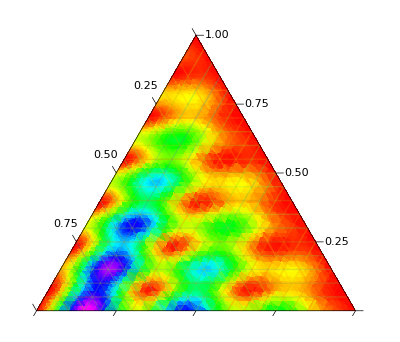

```mathematica
triangleTicks[MapAt[cartestianToBarycentric2@@Transpose[#]&,dp,{1,1}]]
```

## Approach 5: Yet another method

https://mathematica.stackexchange.com/a/39750/60546

```mathematica
(*transform simplex coordinates to cartesian ones*)(*using the following simplex vertices:{{0,0},{1,0},{1/2,Sqrt[3]/2}}*)transform[{x_,y_}]:={1,0,0}+x*{-1,1,0}+y*{-1/Sqrt@3,-1/Sqrt@3,2/Sqrt@3};
```

```mathematica
(*test whether a point is inside the simplex*)
insideQ[pt_List]:=(Total@pt==1&&And@@NonNegative@pt);
```

```mathematica
f1[{p_,q_,r_}]:=r Sin[10 p]^2+(1-r) r Cos[20 q]^2;
```

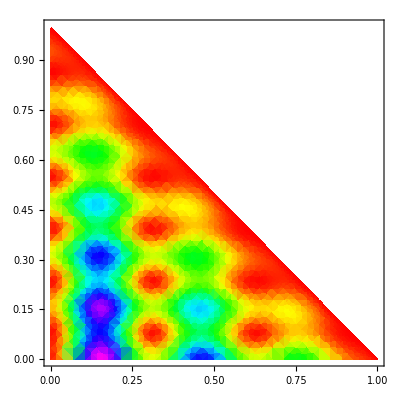
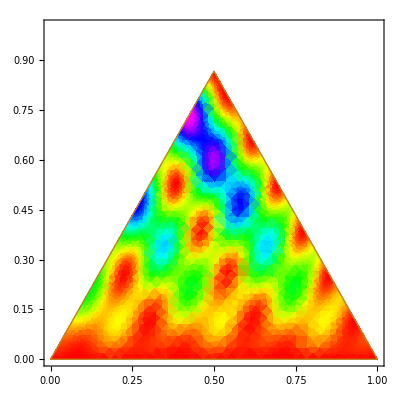

```mathematica
{DensityPlot[f1@{x,y,1-x-y},{x,0,1},{y,0,1},ColorFunction->(Hue[0.85 #]&),RegionFunction->(#1≤1-#2&)],DensityPlot[f1@transform@{x,y},{x,0,1},{y,0,1},ColorFunction->(Hue[0.85 #]&),RegionFunction->(insideQ@transform@{#1,#2}&),BoundaryStyle->Black]}
```